# Running Coupling

```mathematica
ClearAll["Global`*"]
```

## SM parameters

```mathematica
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

## SM Running

$Aborted

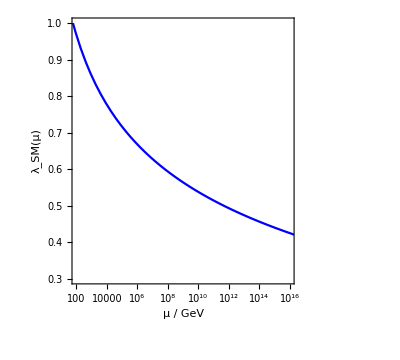

```mathematica
κ=1/(16*Pi^2);

(*numbers of flavors*)
nf=6;
ng=3;

z3=Zeta[3];

(*QCD colour factors*)
ca=3;
dR=3;
cf=4/3;
cr=1/2;


(*Beta function for top-Yukawa*)βyt[λ_,yt_,g3_,g2_,g1_]:=2*yt*(+κ*yt^2*(3/4+1/2*dR)+κ*g3^2*(-3*cf)+κ^2*λ^2*(3)+κ^2*yt^2*λ*(-6)+κ^2*yt^4*(3/4-9/4*dR)+κ^2*g3^2*yt^2*(6*cf+5/2*cf*dR)+κ^2*g3^4*(-3/2*cf^2-97/6*ca*cf+10/3*nf*cr*cf)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*cf)+κ^3*g3^2*yt^4*(-57/2*cf-81/8*cf*dR)+κ^3*g3^4*yt^2*(471/16*cf^2-119/8*cf^2*dR+25*cr*cf+717/16*ca*cf+77/4*ca*cf*dR-33/4*nf*cr*cf-4*nf*cr*cf*dR-27*z3*cf^2+18*z3*cf^2*dR-27/2*z3*ca*cf-9*z3*ca*cf*dR)+κ^3*g3^6*(-129/2*cf^3+129/4*ca*cf^2-11413/108*ca^2*cf+46*nf*cr*cf^2+556/27*nf*ca*cr*cf+140/27*nf^2*cr^2*cf-48*z3*nf*cr*cf^2+48*z3*nf*ca*cr*cf))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge couplings*)
βg3[λ_,yt_,g3_,g2_,g1_]:=2*g3*(+κ*g3^2*(-11/6*ca+2/3*nf*cr)+κ^2*g3^2*yt^2*(-2*cr)+κ^2*g3^4*(-17/3*ca^2+2*nf*cr*cf+10/3*nf*ca*cr)+κ^3*g3^2*yt^4*(9/2*cr+7/2*cr*dR)+κ^3*g3^4*yt^2*(-3*cr*cf-12*ca*cr)+κ^3*g3^6*(-2857/108*ca^3-nf*cr*cf^2+205/18*nf*ca*cr*cf+1415/54*nf*ca^2*cr-22/9*nf^2*cr^2*cf-79/27*nf^2*ca*cr^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9*ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3*ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupling of the scalar field*)
βλ[λ_,yt_,g3_,g2_,g1_]:=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*cf*dR)+κ^2*g3^2*yt^4*(-4*cf*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*cf*dR+288*z3*cf*dR)+κ^3*g3^2*yt^4*λ*(895/4*cf*dR-324*z3*cf*dR)+κ^3*g3^2*yt^6*(-19/2*cf*dR+60*z3*cf*dR)+κ^3*g3^4*yt^2*λ*(-119/2*cf^2*dR+77*ca*cf*dR-16*nf*cr*cf*dR+72*z3*cf^2*dR-36*z3*ca*cf*dR)+κ^3*g3^4*yt^4*(131/2*cf^2*dR+48*cr*cf*dR-109/2*ca*cf*dR+10*nf*cr*cf*dR-48*z3*cf^2*dR+24*z3*ca*cf*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10ng)g2^4-39/4 g2^2 g1^2-(687/200+2ng)25/9 g1^4)2λ+(497/8-8ng)g2^6-(97/40+8/5 ng)5/3 g2^4 g1^2-(717/200+8/5 ng)25/9 g2^2 g1^4-(531/1000+24/25 ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));



(*gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;


tabSMvp={};

For[i=-2,i<3,i++,

mhpole=125.10+0.01*0;
mtpole=172.76+0.3*i;
αsmZ=0.1179+0.0010*(0);
g3mZ=√(4π*αsmZ);



(*MSbar quartic coupling*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);

(*MSbar Yukawa coupling*)ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);

g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;

(*---------calculations of the running parameters-------------*)

(*s=NDSolve[{D[hλ[t,m],t]==βλ[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hyt[t,m],t]==βyt[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg3[t,m],t]==βg3[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg2[t,m],t]==βg2[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg1[t,m],t]==βg1[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],hλ[Log[m/mZ],m]==λmtpole[m],hyt[Log[m/mZ],m]==ytmtpole[m],hg3[0,m]==g3mZ,hg2[0,m]==g2mZ,hg1[0,m]==g1mZ},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},{m,160,180}];*)
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];

λpre0:=hλ/.s;
{λpre1}=λpre0;
λ[t_]:=λpre1[t];
ytpre0:=hyt/.s;
{ytpre1}=ytpre0;
yt[t_]:=ytpre1[t];
g3pre0:=hg3/.s;
{g3pre1}=g3pre0;
g3[t_]:=g3pre1[t];
g2pre0:=hg2/.s;
{g2pre1}=g2pre0;
g2[t_]:=g2pre1[t];
g1pre0:=hg1/.s;
{g1pre1}=g1pre0;
g1[t_]:=g1pre1[t];







Mv[i]=M/.FindRoot[λ[Log[M/mZ]]==0.02,{M,10^11,10^6,Mpl}];



AppendTo[tabSMvp,{mtpole,Log10[Mv[i]]}]


]

λSM=LogLinearPlot[{{λ[Log[x/mZ]]},0},{x,10,10^17},
PlotRange->{{100,10^16},{-0.02,0.16}},
PlotStyle->{Blue,Directive[Black,Dashed]},
AspectRatio->0.9,
Frame-> {{True,True},{True,True}},FrameStyle->Directive[15,Black],
FrameTicksStyle->15,
FrameTicks->{{Automatic,None},{{{10^2,"10^2",{0.02,0.}},{10^5,"10^5",{0.02,0.}},{10^8,"10^8",{0.02,0.}},{10^11,"10^11",{0.02,0.}},{10^14,"10^14",{0.02,0.}}},None}},
PlotRange->{Full,Full},
FrameLabel->  {"μ / GeV","λ_SM(μ)"},
Epilog->{
Inset[Style[Rotate["m_top=173.1 GeV\n α_s(m_Z)=0.1184\n m_h=125.18 GeV",0Degree],FontSize->13],{Log[10^13.3],0.125}]
}
]
ytSM=LogLinearPlot[{{yt[Log[x/mZ]]},0},{x,10,10^17},
PlotRange->{{100,10^16},{0.3,1.0}},
PlotStyle->{Blue,Directive[Black,Dashed]},
AspectRatio->0.9,
Frame-> {{True,True},{True,True}},FrameStyle->Directive[15,Black],
FrameTicksStyle->15,
FrameTicks->{{Automatic,None},{{{10^2,"10^2",{0.02,0.}},{10^5,"10^5",{0.02,0.}},{10^8,"10^8",{0.02,0.}},{10^11,"10^11",{0.02,0.}},{10^14,"10^14",{0.02,0.}}},None}},
PlotRange->{Full,Full},
FrameLabel->  {"μ / GeV","λ_SM(μ)"},
Epilog->{
Inset[Style[Rotate["m_top=173.1 GeV\n α_s(m_Z)=0.1184\n m_h=125.18 GeV",0Degree],FontSize->13],{Log[10^13.3],0.125}]
}
]
```

## Running eq

### Input factors

```mathematica
κ=1/(16 π^2)(*Phase space factor*);
Nf=6;(*number of flavor why?*)
Ng=3;(*number of generation*)
z3=Zeta[3];
(*QCD*)
CA=3;(*Casimir operator Subscript[C, A]=Subscript[C, 2](adj)*)
CF=4/3;(*Casimir operator Subscript[C, F]=Subscript[C, 2](fund)*)
TR=1/2;(*Index Subscript[T, R](fund)*)
dR=3;(*dimension of representation, can be understood as color factor*)
yN=0.65;
SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;
```

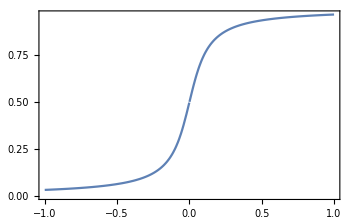

```mathematica
Plot[SmoothUnitStep[x],{x,-1,1}]
```

### Beta functions

Model: Extra vectorlike leptons Lbar, E, L, Ebar. After the first ssb, it becomes charged Dirac fermions. Let’s name them E and Ebar. These both have SM hypercharge Y=±1.

```mathematica
βyt[λ_,yt_,g3_,g2_,g1_]:=2yt(κ yt^2(3/4+1/2 dR)+κ g3^2(-3CF)+3 κ^2 λ^2+(-6)κ^2 yt^2 λ+κ^2 yt^4(3/4-9/4 dR)+κ^2 g3^2 yt^2(6CF+5/2 CF dR)+κ^2 g3^4(-3/2 CF^2-97/6 CA CF+10/3 Nf TR CF)+κ^3 λ^3(-18)+κ^3 yt^2 λ^2(285/8-45/4 dR)+κ^3 yt^4 λ(63/2+45/2 dR)+κ^3 yt^6(-345/32+107/32 dR+39/16 dR^2+9/4 z3+3/2 z3 dR)+κ^3 g3^2 yt^2 λ(6CF)+κ^3 g3^2 yt^4(-57/2 CF-81/8 CF dR)+κ^3 g3^4 yt^2(471/16 CF^2-119/8 CF^2 dR+25TR CF+717/16 CA CF+77/4 CA CF dR-33/4 Nf TR CF-4Nf TR CF dR-27z3 CF^2+18z3 CF^2 dR-27/2 z3 CA CF-9 z3 CA CF dR)+κ^3 g3^6(-129/2 CF^3+129/4 CA CF^2-11413/108 CA^2 CF+46Nf TR CF^2+556/27 Nf CA TR CF+140/27 Nf^2 TR^2 CF-48z3 Nf TR CF^2+48z3 Nf CA TR CF))+
yt κ(-9/4 g2^2-17/12 g1^2)+
yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45 Ng)+58/57 g1^4*2-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-Ng)g2^4+9 g2^2 g3^2);
βg3[λ_,yt_,g3_,g2_,g1_]:=2g3(κ g3^2(-11/6 CA+2/3 Nf TR)+κ^2 g3^2 yt^2(-2TR)+κ^2 g3^4(-17/3 CA^2+2Nf TR CF+10/3 Nf CA TR)+κ^3 g3^2 yt^4(9/2 TR+7/2 TR dR)+κ^3 g3^4 yt^2(-3TR CF-12CA TR)+κ^3 g3^6(-2857/108 CA^3-Nf TR CF^2+205/18 Nf CA TR CF+1415/54 Nf CA^2 TR-22/9 Nf^2 TR^2 CF-79/27 Nf^2 CA TR^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9 Ng+2/3*2)+g1^3 κ^2 5/3(199/30 g1^2+6/5*2 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3 Ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);
βλ[λ_,yt_,g3_,g2_,g1_,t_]:=2(12κ λ^2+2κ yt^2 λ dR+κ yt^4(-dR)+κ (yN SmoothUnitStep[t-Log[500/mZ]])^4(-2)+κ^2 λ^3(-156)+κ^2 yt^2 λ^2(-24dR)+κ^2 yt^4 λ(-1/2 dR)+κ^2 yt^6(5dR)+κ^2 g3^2 yt^2 λ(10CF dR)+κ^2 g3^2 yt^4(-4CF dR)+κ^3 λ^4(3588+2016z3)+κ^3 yt^2 λ^3(291dR)+κ^3 yt^4 λ^2(789/2 dR-36 dR^2+252z3 dR)+κ^3 yt^6 λ(-1881/8 dR+80 dR^2-66z3 dR)+κ^3 yt^8(13/2 dR-195/8 dR^2-12z3 dR)+κ^3 g3^2 yt^2 λ^2(-306CF dR+288z3 CF dR)+κ^3 g3^2 yt^4 λ(895/4 CF dR-324 z3 CF dR)+κ^3 g3^2 yt^6(-19/2 CF dR+60z3 CF dR)+κ^3 g3^2 yt^2 λ(-119/2 CF^2 dR+77CA CF dR-16Nf TR CF dR+72z3 CF^2 dR-36z3 CA CF dR)+κ^3 g3^4 yt^4(131/2 CF^2 dR+48TR CF dR-109/2 CA CF dR+10Nf TR CF dR-48z3 CF^2 dR+24z3 CA CF dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10Ng)g2^4-39/4 g2^2 g1^2-(687/200+2Ng)25/9 g1^4+60/19*2 g1^4)2λ+(497/8-8Ng)g2^6-(97/40+8/5 Ng)5/3 g2^4 g1^2-(717/200+8/5 Ng)25/9 g2^2 g1^4-(531/1000+24/25 Ng)125/27 g1^6-1728/505*2 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10 *2 λ yt^2(17/12 g1^2+9/4 g2^2));
```

```mathematica
25/9*29/45
```

145/81

```mathematica
(1/6)^2*2+(2/3)^2+(1/3)^2
```

11/18

```mathematica
3*(2*(1/6)^2+(2/3)^2+(1/3)^2)+2(1/2)^2+1
```

10/3

```mathematica
3*(2*(1/6)^4+(2/3)^4+(1/3)^4)+2(1/2)^4+1
```

95/54

```mathematica
3*(2*(1/6)^6+(2/3)^6+(1/3)^6)+2(1/2)^6+1
```

2525/1944

```mathematica
24/25*125/27/(2525/1944)
```

1728/505

```mathematica
50/9/(95/54)
```

60/19

```mathematica
3*(1/6)^2+(1/2)^2
```

1/3

```mathematica
145/81/(95/54)
```

58/57

```mathematica
19/15*25/9(*Fermion contribution to g1^5 from 2-loop paper*)
```

95/27

```mathematica
3*95/27+1/2(*total contribution to g1^5 from the 2-loop paper*)
```

199/18

```mathematica
5/3*199/30(*total contribution to g1^5 from the code above*)
```

199/18

## Solve the Running

```mathematica
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;


tabSMvp={};

For[i=-2,i<3,i++,

mhpole=125.10+0.01*0;
mtpole=172.76+0.3*i;
αsmZ=0.1179+0.0010*(0);
g3mZ=√(4π*αsmZ);



(*MSbar quartic coupling*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);

(*MSbar Yukawa coupling*)ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);

g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;

(*---------calculations of the running parameters-------------*)

(*s=NDSolve[{D[hλ[t,m],t]==βλ[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hyt[t,m],t]==βyt[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg3[t,m],t]==βg3[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg2[t,m],t]==βg2[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg1[t,m],t]==βg1[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],hλ[Log[m/mZ],m]==λmtpole[m],hyt[Log[m/mZ],m]==ytmtpole[m],hg3[0,m]==g3mZ,hg2[0,m]==g2mZ,hg1[0,m]==g1mZ},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},{m,160,180}];*)
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],t],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];

λpre0:=hλ/.s;
{λpre1}=λpre0;
λ[t_]:=λpre1[t];
ytpre0:=hyt/.s;
{ytpre1}=ytpre0;
yt[t_]:=ytpre1[t];
g3pre0:=hg3/.s;
{g3pre1}=g3pre0;
g3[t_]:=g3pre1[t];
g2pre0:=hg2/.s;
{g2pre1}=g2pre0;
g2[t_]:=g2pre1[t];
g1pre0:=hg1/.s;
{g1pre1}=g1pre0;
g1[t_]:=g1pre1[t];
Mv[i]=M/.FindRoot[λ[Log[M/mZ]]==0.02,{M,10^11,10^4,Mpl}];
AppendTo[tabSMvp,{mtpole,Log10[Mv[i]]}]
]
```

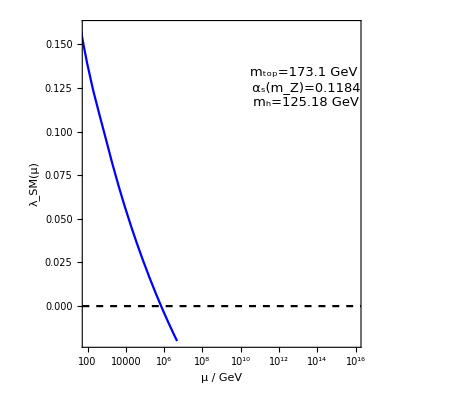

```mathematica
λnew=LogLinearPlot[{{λ[Log[x/mZ]]},0},{x,10,10^17},
PlotRange->{{100,10^16},{-0.02,0.16}},
PlotStyle->{Blue,Directive[Black,Dashed]},
AspectRatio->0.9,
Frame-> {{True,True},{True,True}},FrameStyle->Directive[15,Black],
FrameTicksStyle->15,
FrameTicks->{{Automatic,None},{{{10^2,"10^2",{0.02,0.}},{10^5,"10^5",{0.02,0.}},{10^8,"10^8",{0.02,0.}},{10^11,"10^11",{0.02,0.}},{10^14,"10^14",{0.02,0.}}},None}},
PlotRange->{Full,Full},
FrameLabel->  {"μ / GeV","λ_SM(μ)"},
Epilog->{
Inset[Style[Rotate["m_top=173.1 GeV\n α_s(m_Z)=0.1184\n m_h=125.18 GeV",0Degree],FontSize->13],{Log[10^13.3],0.125}]
}
]
```

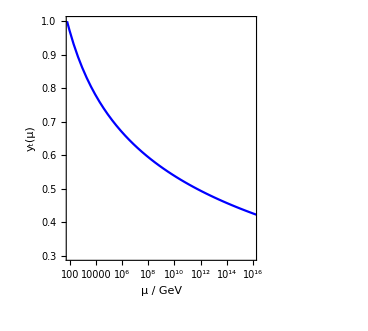

```mathematica
ytnew=LogLinearPlot[{{yt[Log[x/mZ]]},0},{x,10,10^17},
PlotRange->{{100,10^16},{0.3,1.0}},
PlotStyle->{Blue,Directive[Black,Dashed]},
AspectRatio->0.9,
Frame-> {{True,True},{True,True}},FrameStyle->Directive[15,Black],
FrameTicksStyle->15,
FrameTicks->{{Automatic,None},{{{10^2,"10^2",{0.02,0.}},{10^5,"10^5",{0.02,0.}},{10^8,"10^8",{0.02,0.}},{10^11,"10^11",{0.02,0.}},{10^14,"10^14",{0.02,0.}}},None}},
PlotRange->{Full,Full},
FrameLabel->  {"μ / GeV","y_t(μ)"},
Epilog->{
Inset[Style[Rotate["m_top=173.1 GeV\n α_s(m_Z)=0.1184\n m_h=125.18 GeV",0Degree],FontSize->13],{Log[10^13.3],0.125}]
}
]
```

```mathematica
yt[Log[(5*10^5)/mZ]]
```

0.681772

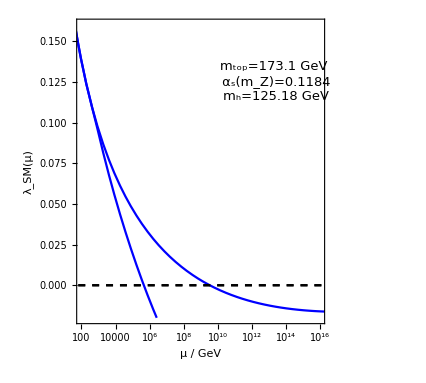

```mathematica
Show[λSM,λnew]
```

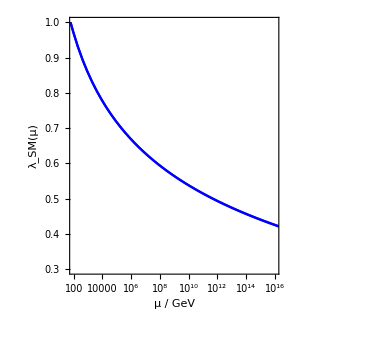

```mathematica
Show[ytSM,ytnew]
```

```mathematica
yt[5]
```

0.768144

```mathematica
Solve[λ[Log[x/mZ]]==0.02,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→8.96019×10^6}}